```mathematica
Clear["Global`*"]
```

# TTV periodogram

```mathematica
thisfolder=NotebookDirectory[];
```

### Get Linear Ephemeris

```mathematica
LRVplan=Import[StringJoin[thisfolder,"LRVplan-stats.dat"],"Table"];
MAPplan=LRVplan[[First[First[Position[LRVplan,{"MAP","Parameters"}]]]+2;;All]];nparamorig=Last[MAPplan][[1]];
```

```mathematica
Pglob=MAPplan[[4]][[2]]
τglob=MAPplan[[5]][[2]]
```

49.607588509721104

54971.414858511358

### Get Transit Times

```mathematica
data1=Import[StringJoin[thisfolder,"TTVplan1-post_equal_weights.dat"],"Table"];
sdim1=Last[Dimensions[data1]]-1
Dimensions[data1]
```

17

{41277,18}

```mathematica
data2=Import[StringJoin[thisfolder,"TTVplan2-post_equal_weights.dat"],"Table"];
sdim2=Last[Dimensions[data2]]-1
Dimensions[data2]
```

16

{36692,17}

```mathematica
data3=Import[StringJoin[thisfolder,"TTVplan3-post_equal_weights.dat"],"Table"];
sdim3=Last[Dimensions[data3]]-1
Dimensions[data3]
```

16

{31976,17}

```mathematica
j=0;k=0;Label[jloop];j=j+1;k=k+1;Subscript[τtab, k]=data1[[All,nparamorig+j]];If[nparamorig+j<sdim1,Goto[jloop]];
k
j=0;Label[jloop];j=j+1;k=k+1;Subscript[τtab, k]=data2[[All,nparamorig+j]];If[nparamorig+j<sdim2,Goto[jloop]];
k
j=0;Label[jloop];j=j+1;k=k+1;Subscript[τtab, k]=data3[[All,nparamorig+j]];If[nparamorig+j<sdim3,Goto[jloop]];
nepochs=k
```

10

19

28

### Get Mazeh Times

```mathematica
mazehdatabase=Import["~/mazeh_analysis/ttvs.txt","Table"];
```

```mathematica
temp=StringSplit[thisfolder,"/"];
mazehsub=Select[mazehdatabase,#[[1]]==ToExpression[StringSplit[temp[[Length[temp]-1]],"-"][[2]]]&];
```

```mathematica
timesM=Table[{mazehsub[[i,2]],54900+mazehsub[[i,3]]+mazehsub[[i,4]]/(24*60),mazehsub[[i,5]]/(24*60)},{i,1,Length[mazehsub]}];
"adjust epoch numbers...";
timesM=Sort[Table[{Round[(timesM[[j,2]]-τglob)/Pglob],timesM[[j,2]],timesM[[j,3]],timesM[[j,3]]},{j,1,Length[timesM]}]];
```

### Format times and TTVs

```mathematica
timesK=Sort[Table[{Round[(Median[Subscript[τtab, j]]-τglob)/Pglob],Median[Subscript[τtab, j]],Median[Subscript[τtab, j]]-Quantile[Subscript[τtab, j],0.5-0.5Erf[1/√2]],Quantile[Subscript[τtab, j],0.5+0.5Erf[1/√2]]-Median[Subscript[τtab, j]]},{j,1,nepochs}]];
```

```mathematica
rawTTVsM=Table[{timesM[[i,1]],timesM[[i,2]],24*60(timesM[[i,2]]-timesM[[i,1]] Pglob-τglob),24*60timesM[[i,3]],24*60timesM[[i,4]]},{i,1,Length[timesM]}];
rawTTVsK=Table[{timesK[[i,1]],timesK[[i,2]],24*60(timesK[[i,2]]-timesK[[i,1]] Pglob-τglob),24*60timesK[[i,3]],24*60timesK[[i,4]]},{i,1,Length[timesK]}];
```

```mathematica
"Estimate maximum expected level of scatter";
κM=StandardDeviation[rawTTVsM[[All,3]]]
σrescaleM=√(StandardDeviation[rawTTVsM[[All,3]]]/√(Sum[(rawTTVsM[[i,4]])^2,{i,1,Length[rawTTVsM]}]/Length[rawTTVsM]));
ΥM=1/(√(2(Length[rawTTVsM]-1)))√(Sum[(σrescaleM rawTTVsM[[i,4]])^4,{i,1,Length[rawTTVsM]}]/Sum[(σrescaleM rawTTVsM[[i,4]])^2,{i,1,Length[rawTTVsM]}])
extremeM=κM+5ΥM
```

10.2089

2.04164

20.4171

```mathematica
"flag any TTVs from K for which the measurement is outside the extreme value (unreliable), or both errors exceed that level (not useful)";
badepochsK=Select[rawTTVsK,((#[[4]]>extremeM)&&(#[[5]]>extremeM))&][[All,1]]
Length[badepochsK]
badepochsM=Select[rawTTVsM,((#[[4]]>extremeM)&&(#[[5]]>extremeM))&][[All,1]]
Length[badepochsM]
```

{10,21,27}

3

{21}

1

```mathematica
"remove bad epochs";
TTVsK=Select[rawTTVsK,!MemberQ[badepochsK,#[[1]]]&];
TTVsM=Select[rawTTVsM,!MemberQ[badepochsM,#[[1]]]&];
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
offset=0.1;
Kplot=Table[{{TTVsK[[i,1]]-offset,TTVsK[[i,3]]},ErrorBar[{-TTVsK[[i,4]],TTVsK[[i,5]]}]},{i,1,Length[TTVsK]}];
Mplot=Table[{{TTVsM[[i,1]]+offset,TTVsM[[i,3]]},ErrorBar[{-TTVsM[[i,4]],TTVsM[[i,5]]}]},{i,1,Length[TTVsM]}];
```

```mathematica
buffer=0.1;{Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-0.5buffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]),Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]+0.5buffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]])}
```

{-1.45,30.45}

40.3913

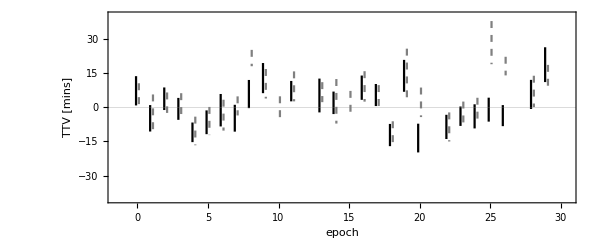

```mathematica
ybuffer=1.25;
yrange=Max[Max[-Min[TTVsK[[All,3]]-ybuffer TTVsK[[All,4]]],Max[TTVsK[[All,3]]+ybuffer TTVsK[[All,5]]]],
Max[-Min[TTVsM[[All,3]]-ybuffer TTVsM[[All,4]]],Max[TTVsM[[All,3]]+ybuffer TTVsM[[All,5]]]]]
xbuffer=0.1;xrange={Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-0.5xbuffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]),Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]+0.5xbuffer(Max[Join[TTVsK[[All,1]],TTVsM[[All,1]]]]-Min[Join[TTVsK[[All,1]],TTVsM[[All,1]]]])};
ttvplotK=ErrorListPlot[Kplot,Frame->True,Axes->None,PlotRange->{xrange,{-yrange,yrange}},GridLines->{{},{0}},AspectRatio->0.4,ImageSize->{600,Automatic},FrameLabel->{"epoch","TTV [mins]"},BaseStyle->{FontFamily->"CMU Serif",FontSize->24},PlotStyle->Black,Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing;
ttvplotM=ErrorListPlot[Mplot,Frame->True,Axes->None,PlotRange->{xrange,{-yrange,yrange}},GridLines->{{},{0}},AspectRatio->0.4,ImageSize->{600,Automatic},FrameLabel->{"epoch","TTV [mins]"},BaseStyle->{FontFamily->"CMU Serif",FontSize->24},PlotStyle->Directive[Dashed,Gray],Joined->True]/.Line[pts:{{x1_?NumericQ,_},{x2_,_},{_,_}...}]/;x1≠x2->Nothing;
dataplot=Show[ttvplotM,ttvplotK]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"TTVsK.dat"],TTVsK,"Table"]
Export[StringJoin[NotebookDirectory[],"TTVsM.dat"],TTVsM,"Table"]
```

### LATEX table

```mathematica
timey=Table[{TTVsK[[i,1]],TTVsK[[i,2]]-55000,N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440],TTVsK[[i,3]],TTVsK[[i,4]],TTVsK[[i,5]]},{i,1,Length[TTVsK]}];
j=0;Label[jloop];j=j+1;dp=Length[Characters[ToString[N[Min[timey[[j,3]],timey[[j,4]]],2]]]]-5;rp=Length[Characters[ToString[Round[timey[[j,2]]]]]];dpx=Length[Characters[ToString[N[Min[timey[[j,6]],timey[[j,7]]],2]]]]-2;rpx=Length[Characters[ToString[Round[timey[[j,5]]]]]];Subscript[α, j]={timey[[j,1]],ToString[N[Round[timey[[j,2]],10^(-dp)],dp+rp+0]],ToString[N[Round[timey[[j,3]],10^(-dp)],dp-2]],ToString[N[Round[timey[[j,4]],10^(-dp)],dp-2]]};Subscript[β, j]={ToString[N[Round[timey[[j,5]],10^(-dpx)],dpx+1]],ToString[N[Round[timey[[j,6]],10^(-dpx)],dpx+1]],ToString[N[Round[timey[[j,7]],10^(-dpx)],dpx+1]]};If[j<Length[timey],Goto[jloop]];
tabby=Table[{Subscript[α, j][[1]],Subscript[α, j][[2]],Subscript[α, j][[3]],Subscript[α, j][[4]],Subscript[β, j][[1]],Subscript[β, j][[2]],Subscript[β, j][[3]]},{j,1,Length[timey]}];
tabby=Table[StringJoin["$",ToString[Subscript[α, j][[1]]],"$ & $",Subscript[α, j][[2]],"_{-",Subscript[α, j][[3]],"}^{+",Subscript[α, j][[4]],"}$ & $",Subscript[β, j][[1]],"_{-",Subscript[β, j][[2]],"}^{+",Subscript[β, j][[3]],"}$"],{j,1,Length[timey]}]
```

{$0$ & $-28.580140_{-0.00440}^{+0.00455}$ & $7.2_{-6.3}^{+6.6}$,$1$ & $21.01915_{-0.00407}^{+0.00401}$ & $-4.8_{-5.9}^{+5.8}$,$2$ & $70.63251_{-0.00328}^{+0.00362}$ & $3.6_{-4.7}^{+5.2}$,$3$ & $120.23724_{-0.00341}^{+0.00329}$ & $-0.60_{-4.9}^{+4.7}$,$4$ & $169.83763_{-0.00304}^{+0.00296}$ & $-11._{-4.4}^{+4.3}$,$5$ & $219.44811_{-0.00350}^{+0.00377}$ & $-6.8_{-5.0}^{+5.4}$,$6$ & $269.05916_{-0.00459}^{+0.00533}$ & $-1.8_{-6.6}^{+7.7}$,$7$ & $318.66461_{-0.00405}^{+0.00416}$ & $-4.8_{-5.8}^{+6.0}$,$8$ & $368.27949_{-0.00415}^{+0.00446}$ & $5.7_{-6.0}^{+6.4}$,$9$ & $417.8918_{-0.0043}^{+0.0049}$ & $12._{-6.2}^{+7.1}$,$11$ & $517.10330_{-0.00312}^{+0.00312}$ & $7.2_{-4.5}^{+4.5}$,$13$ & $616.31704_{-0.00506}^{+0.00528}$ & $5.1_{-7.3}^{+7.6}$,$14$ & $665.92228_{-0.00322}^{+0.00366}$ & $1.7_{-4.6}^{+5.3}$,$16$ & $765.14237_{-0.00378}^{+0.00364}$ & $8.8_{-5.4}^{+5.2}$,$17$ & $814.74774_{-0.00346}^{+0.00328}$ & $5.6_{-5.0}^{+4.7}$,$18$ & $864.34294_{-0.00334}^{+0.00345}$ & $-12._{-4.8}^{+5.0}$,$19$ & $913.96884_{-0.00503}^{+0.00473}$ & $14._{-7.2}^{+6.8}$,$20$ & $963.55778_{-0.00492}^{+0.00387}$ & $-13._{-7.1}^{+5.6}$,$22$ & $1062.7756_{-0.0034}^{+0.0040}$ & $-9.0_{-4.9}^{+5.7}$,$23$ & $1112.3866_{-0.0029}^{+0.0030}$ & $-4.0_{-4.2}^{+4.4}$,$24$ & $1161.99431_{-0.00376}^{+0.00362}$ & $-3.9_{-5.4}^{+5.2}$,$25$ & $1211.60380_{-0.00358}^{+0.00374}$ & $-1.1_{-5.2}^{+5.4}$,$26$ & $1261.20972_{-0.00329}^{+0.00314}$ & $-3.5_{-4.7}^{+4.5}$,$28$ & $1360.43130_{-0.00445}^{+0.00445}$ & $5.7_{-6.4}^{+6.4}$,$29$ & $1410.0480_{-0.0053}^{+0.0053}$ & $19._{-7.7}^{+7.7}$}

```mathematica
Export[StringJoin[thisfolder,"times_table.tex"],tabby,"Table"]
```

## Periodogram

### Start with null model, a simple linear ephemeris...

```mathematica
χ2fn[input_,predictions_]:=Sum[Piecewise[{{((input[[i,1]]-predictions[[i]])/input[[i,3]])^2,(input[[i,1]]-predictions[[i]])<0},{((input[[i,1]]-predictions[[i]])/input[[i,2]])^2,(input[[i,1]]-predictions[[i]])>0}}],{i,1,Length[input]}];
```

```mathematica
"using global ephemeris, this gives...";
χ2fn[TTVsK[[All,{3,4,5}]],Table[0,{i,1,Length[TTVsK]}]]
```

49.7118227

```mathematica
"but really we should fit a linear ephemeris anew, to fully replicate the LS proceedure";
linearmodel[θ_,t_]:=θ[[1]] t+θ[[2]]
```

```mathematica
"check it gives the same answer...";
χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[linearmodel[{Pglob,τglob},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]]
```

49.7118

```mathematica
"find best fitting ephemeris for K data";
testfnK[P_,τ_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[linearmodel[{P,τ},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];
bartab={{Pglob,τglob}};
minnyK=NMinimize[{testfnK[P,τ],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ},Method->{"Automatic","InitialPoints"->bartab}];
χ2nullK=minnyK[[1]]
PfitK=minnyK[[2]][[All,2]][[1]]
τfitK=minnyK[[2]][[All,2]][[2]]
```

49.6054

49.6076

54971.4

```mathematica
"find best fitting ephemeris for M data";
testfnM[P_,τ_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[linearmodel[{P,τ},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];
bartab={{Pglob,τglob}};
minnyM=NMinimize[{testfnM[P,τ],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ},Method->{"Automatic","InitialPoints"->bartab}];
χ2nullM=minnyM[[1]]
PfitM=minnyM[[2]][[All,2]][[1]]
τfitM=minnyM[[2]][[All,2]][[2]]
```

71.7082

49.6077

54971.4

### K first

```mathematica
"define the new model";
sinusoidmodel[θ_,t_]:=θ[[1]] t+θ[[2]]+θ[[3]] Sin[(2π t)/θ[[5]]]+θ[[4]] Cos[(2π t)/θ[[5]]];
```

```mathematica
"define properties of the LS periodogram";
temp=Sort[TTVsK];
minP=2Min[Table[temp[[i+1,1]]-temp[[i,1]],{i,1,Length[temp]-1}]];
maxP=2(Max[temp[[All,1]]]-Min[temp[[All,1]]]);
minν=1/maxP;maxν=1/minP;
ngrid=10Length[temp];
νgrid=N[Table[ν,{ν,minν,maxν,(maxν-minν)/ngrid}]][[1;;ngrid]];
Pgrid=Table[1/νgrid[[i]],{i,1,Length[νgrid]}];
```

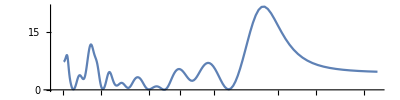

```mathematica
tstart=AbsoluteTime[];j=0;Label[jloop];j=j+1;Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[sinusoidmodel[{P,τ,A1,A2,Pgrid[[j]]},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];bartab={{Pglob,τglob,0,0}};minnyK=NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];Subscript[α, j]={minnyK[[1]],1440 √(minnyK[[2]][[All,2]][[3]]^2+minnyK[[2]][[All,2]][[4]]^2)};If[j<Length[Pgrid],Goto[jloop]];tend=AbsoluteTime[];timeperLS=tend-tstart;
lombscargleK=Table[{Pgrid[[jj]],χ2nullK-Subscript[α, jj][[1]],Subscript[α, jj][[2]]},{jj,1,Length[Pgrid]}];
ListLogLinearPlot[lombscargleK[[All,{1,2}]],PlotRange->All,Joined->True,AspectRatio->0.25]
```

```mathematica
bestPK=Select[lombscargleK,#[[2]]==Max[lombscargleK[[All,2]]]&]
bestΔχ2K=bestPK[[1]][[2]]
bestAK=bestPK[[1]][[3]]
bestPK=bestPK[[1]][[1]]
bestΔBICK=bestΔχ2K-3 Log[Length[TTVsK]]
```

{{17.3031,21.6232,8.1737}}

21.6232

8.1737

17.3031

11.9666

```mathematica
Clear[testfnK];testfnK[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsK[[i,2]],N[TTVsK[[i,4]]/1440],N[TTVsK[[i,5]]/1440]},{i,1,Length[TTVsK]}],Table[sinusoidmodel[{P,τ,A1,A2,bestPK},TTVsK[[i,1]]],{i,1,Length[TTVsK]}]];bartab={{Pglob,τglob,0,0}};minnyK=NMinimize[{testfnK[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];
bestθK=minnyK[[2]][[All,2]]
bestsinusoidK[t_]:=bestθK[[1]] t+bestθK[[2]]+bestθK[[3]] Sin[(2π t)/bestPK]+bestθK[[4]] Cos[(2π t)/bestPK];
```

{49.6075,54971.4,-0.00564818,-0.000563128}

### M first

```mathematica
"define properties of the LS periodogram";
temp=Sort[TTVsM];
minP=2Min[Table[temp[[i+1,1]]-temp[[i,1]],{i,1,Length[temp]-1}]];
maxP=2(Max[temp[[All,1]]]-Min[temp[[All,1]]]);
minν=1/maxP;maxν=1/minP;
ngrid=10Length[temp];
νgrid=N[Table[ν,{ν,minν,maxν,(maxν-minν)/ngrid}]][[1;;ngrid]];
Pgrid=Table[1/νgrid[[i]],{i,1,Length[νgrid]}];
```

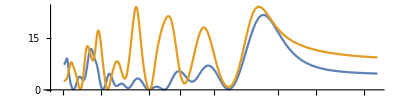

```mathematica
j=0;Label[jloop];j=j+1;Clear[testfnM];testfnM[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[sinusoidmodel[{P,τ,A1,A2,Pgrid[[j]]},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];bartab={{Pglob,τglob,0,0}};minnyM=NMinimize[{testfnM[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];Subscript[α, j]={minnyM[[1]],1440 √(minnyM[[2]][[All,2]][[3]]^2+minnyM[[2]][[All,2]][[4]]^2)};If[j<Length[Pgrid],Goto[jloop]];
lombscargleM=Table[{Pgrid[[jj]],χ2nullM-Subscript[α, jj][[1]],Subscript[α, jj][[2]]},{jj,1,Length[Pgrid]}];
ListLogLinearPlot[{lombscargleK[[All,{1,2}]],lombscargleM[[All,{1,2}]]},PlotRange->All,Joined->True,AspectRatio->0.25]
```

```mathematica
bestPM=Select[lombscargleM,#[[2]]==Max[lombscargleM[[All,2]]]&]
bestΔχ2M=bestPM[[1]][[2]]
bestAM=bestPM[[1]][[3]]
bestPM=bestPM[[1]][[1]]
bestΔBICM=bestΔχ2M-3 Log[Length[TTVsM]]
```

{{16.1443,24.0302,8.82696}}

24.0302

8.82696

16.1443

14.1427

```mathematica
Clear[testfnM];testfnM[P_,τ_,A1_,A2_]:=χ2fn[Table[{TTVsM[[i,2]],N[TTVsM[[i,4]]/1440],N[TTVsM[[i,5]]/1440]},{i,1,Length[TTVsM]}],Table[sinusoidmodel[{P,τ,A1,A2,bestPM},TTVsM[[i,1]]],{i,1,Length[TTVsM]}]];bartab={{Pglob,τglob,0,0}};minnyM=NMinimize[{testfnM[P,τ,A1,A2],Pglob-1<P<Pglob+1,τglob-1<τ<τglob+1},{P,τ,A1,A2},Method->{"NelderMead","InitialPoints"->bartab}];
bestθM=minnyM[[2]][[All,2]]
bestsinusoidM[t_]:=bestθM[[1]] t+bestθM[[2]]+bestθM[[3]] Sin[(2π t)/bestPM]+bestθM[[4]] Cos[(2π t)/bestPM];
```

{49.6075,54971.4,-0.00570444,-0.0022437}

### PLOT THE RESULTS

```mathematica
N[3 Log[Length[TTVsK]]]
```

9.65663

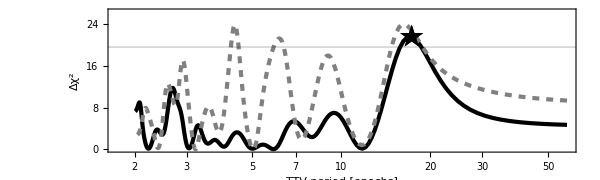

```mathematica
Yrange={0,1.1Max[Max[lombscargleK[[All,2]]],Max[lombscargleM[[All,2]]]]};
tempK={{bestPK,bestΔχ2K}};
tempM={{bestPM,bestΔχ2M}};
LSplot=Show[ListLogLinearPlot[lombscargleK[[All,{1,2}]],PlotRange->{All,Yrange},Frame->True,FrameLabel->{"TTV period [epochs]","Δχ^2"},AspectRatio->0.3,Joined->True,PlotStyle->Directive[Black,Thickness[0.005]],ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None,GridLines->{{},{{N[3 Log[Length[TTVsK]]]+10,Directive[Black]}}}],ListLogLinearPlot[lombscargleM[[All,{1,2}]],PlotRange->All,Frame->True,FrameLabel->{"TTV period [epochs]","Δχ^2"},AspectRatio->0.3,Joined->True,PlotStyle->Directive[Gray,Dashed,Thickness[0.005]],ImageSize->{600,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},Axes->None],ListLogLinearPlot[tempK,PlotMarkers->{"★",25},PlotStyle->Black]]
```

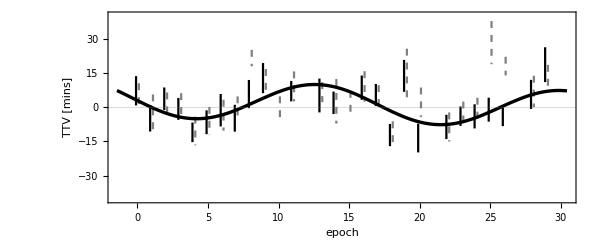

```mathematica
finalttvplot=Show[dataplot,Plot[1440(bestsinusoidK[t]-linearmodel[{Pglob,τglob},t]),{t,xrange[[1]],xrange[[2]]},PlotStyle->Directive[Black,Thickness[0.004],Opacity[1]]]]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"periodogram.pdf"],LSplot]
Export[StringJoin[NotebookDirectory[],"TTVs.pdf"],finalttvplot]
```

```mathematica
bestfitmodel=Table[{timey[[i,1]],linearmodel[{Pglob,τglob},timey[[i,1]]],1440(bestsinusoidK[timey[[i,1]]]-linearmodel[{Pglob,τglob},timey[[i,1]]])},{i,1,Length[timey]}]
```

{{0,54971.414858511358,3.00467},{1,55021.022447021079,0.0171927},{2,55070.6300355308,-2.49466},{3,55120.237624040521,-4.22304},{4,55169.845212550242,-4.96228},{5,55219.452801059964,-4.63573},{6,55269.060389569685,-3.30571},{7,55318.667978079406,-1.16543},{8,55368.275566589127,1.48623},{9,55417.883155098848,4.28372},{11,55517.09833211829,8.80894},{13,55616.313509137732,9.97372},{14,55665.921097647453,8.9806},{16,55765.136274666896,4.37788},{17,55814.743863176617,1.32906},{18,55864.351451686338,-1.73115},{19,55913.959040196059,-4.4234},{20,55963.56662870578,-6.41632},{22,56062.781805725222,-7.46604},{23,56112.389394234943,-6.42543},{24,56161.996982744665,-4.50337},{25,56211.604571254386,-1.97028},{26,56261.212159764107,0.823733},{28,56360.427336783549,5.67407},{29,56410.03492529327,7.05834}}

```mathematica
Export[StringJoin[NotebookDirectory[],"bestfitmodel.dat"],bestfitmodel,"Table"]
```